# Examen parcial I

## Pregunta 1

Grafica el espacio fase del sistema  y usándolo encuentra todas sus soluciones de equilibrio y determina su estabilidad.

Solución:
 es la única solución de equilibrio y es estable.

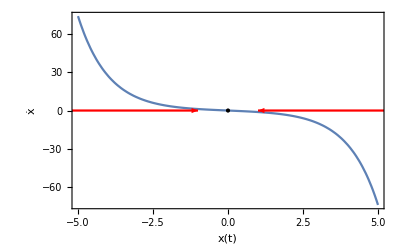

```mathematica
p1=Show[Plot[-Sinh[x],{x,-5,5},Frame->{True,True,False,False},FrameLabel->{x[t],OverDot[x]},Epilog->{PointSize[Medium],Point[{{0,0}}]}],NumberLinePlot[Interval[{-6,Infinity}],{x,-6,-1},PlotStyle->Red,Spacings->0],NumberLinePlot[Interval[{-Infinity,6}],{x,1,6},PlotStyle->Red,Spacings->0]]
```

## Pregunta 2

Usando sólo las gráficas de  y  estima el valor de los primeros cuatro puntos de equilibrio del sistema  más cercanos a  y determina su estabilidad.

Solución:
Las soluciones de equilibrio y su estabilidad son:

estable pues  después del punto y viceversa antes del punto.

inestable pues  antes del punto y viceversa después del punto.

estable pues  después del punto y viceversa antes del punto.

inestable pues  antes del punto y viceversa después del punto.

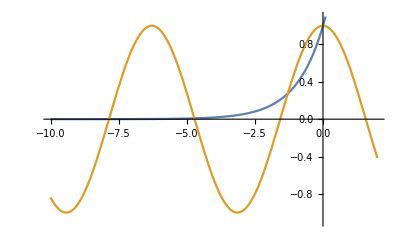

```mathematica
p2=Plot[{Exp[x],Cos[x]},{x,-10,2},PlotRange->{{-10,2},{-1.1,1.1}}]
```

## Pregunta 3

Explica porqué el sistema dinámico  con condiciones iniciales  no tiene solución.

Solución:
La función  no toma valores reales en .

## Pregunta 4

Muestra que la función  definida como

```mathematica
TraditionalForm[x[t]==Piecewise[{{0,0<t<1},{(t-1)^3,1<=t<2}}]]
```

x(t)==(Piecewise[{{0, 0<t<1}, {(t-1)^3, 1≤t<2}}])

es diferenciable en  y es solución del sistema dinámico  con condiciones iniciales 

Solución:
Es diferenciable pues 1)  y  son diferenciables y en el punto donde se unen los dos trozos de la función, , las derivadas coinciden como se puede ver aquí:

```mathematica
D[0,t]/.{t->1}
```

0

```mathematica
D[(t-1)^3,t]/.{t->1}
```

0

La solución cumple con las condiciones iniciales pues efectivamente  y si sustituimos en la ecuación vemos que se cumple la igualdad como se ve a continuación:

```mathematica
D[0,t]
```

0

```mathematica
3*(0)^(2/3)
```

0

```mathematica
D[(t-1)^3,t]
```

3 (-1+t)^2

```mathematica
PowerExpand[3*(((t-1)^3)^(2/3))]
```

3 (-1+t)^2

## Pregunta 5

El sistema dinámico , con  y  dos constantes positivas es comúnmente usado para modelar poblaciones de instectos. Recordando que las densidades de población sólo pueden ser cantidades no negativas, explica qué tendencia poblacional predice el modelo en el límite , con respecto a los valores de  y , de acuerdo al análisis de estabilidad lineal.

Solución:
En este caso, tenemos que el lado derecho de la igualdad es la función . Primero necesitamos encontrar las soluciones de equilibrio, las cuales obedecen la relación :

```mathematica
Solve[r*x/(x+A)-x==0,x]
```

{{x→0},{x→-A+r}}

Vemos que tiene dos soluciones de equilibrio,  y . Para determinar su estabilidad, necesitamos evaluar la derivada de la función  en cada punto de equilibrio. Encontramos que, para cada uno:

```mathematica
D[r*x/(x+A)-x,x]/.{x->0}
```

-1+r/A

```mathematica
D[r*x/(x+A)-x,x]/.{x->r-A}
```

-(-A+r)/r

Para que la solución  sea estable, necesitamos entonces que , o despejando, . Por otro lado, para que la solución  sea estable, necesitamos que , o puesto de otra forma, , tomando en cuenta que . Sus condiciones de equilibrio son contrarias, por lo que, cuando una es estable, la otra es inestable y viceversa. Como no hay otra solución de equilibrio, en el límite cuando  sólo pueden pasar 2 cosas (tomando en cuenta que sólo tiene sentido que las condiciones iniciales ).

La población tiende a cero cuando  tiende a infinito si , puesto que  es estable y el segundo punto de equilibrio, <0.

La población tiende a  cuando  tiende a infinito si , puesto que  es estable y positiva.

## Pregunta 6

Considera el sistema , donde ,  y  son constantes tales que , con condiciones iniciales , .

Grafica el campo de pendientes y el espacio fase. Para cada  posible, usa la información de estas dos gráficas para determinar el comportamiento de las soluciones cuando . Considera los casos ,  y .

Resuelve la ecuación diferencial de forma exacta (tomando en cuenta las condiciones iniciales) usando fracciones parciales. Verifica que el comportamiento de estas expresiones concuerde con el que encontraste cualitativamente en el inciso anterior.

Usando las soluciones exactas del inciso anterior, muestra que si  y , ó si  y , las soluciones explotan en un tiempo positivo finito. Encuentra el intervalo máximo  en el cual existe la solución.

Solución:

Campos de pendientes y espacios fase:

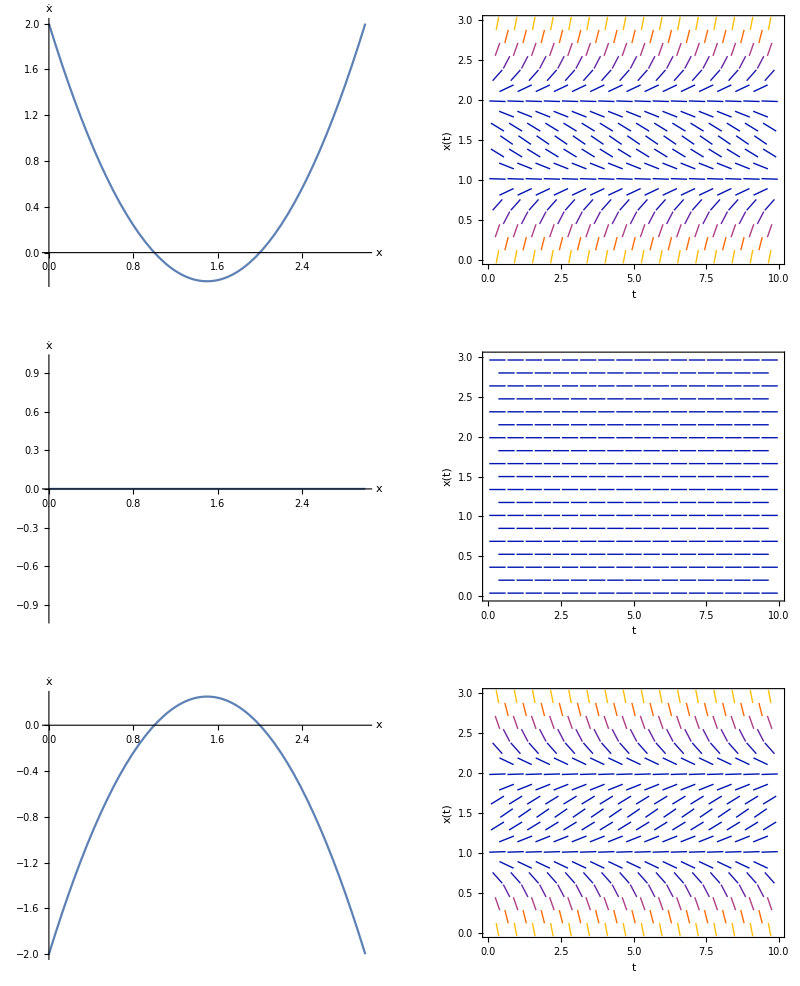

```mathematica
GraphicsGrid[{{Plot[(x-1)*(x-2),{x,0,3},AxesLabel->{x,OverDot[x]}],VectorPlot[{1,(x-1)*(x-2)},{t,0,10},{x,0,3},AxesLabel->{t,x[t]},VectorStyle->Arrowheads[0]]},{Plot[0*(x-1)*(x-2),{x,0,3},AxesLabel->{x,OverDot[x]}],VectorPlot[{1,0*(x-1)*(x-2)},{t,0,10},{x,0,3},AxesLabel->{t,x[t]},VectorStyle->Arrowheads[0]]},{Plot[-1*(x-1)*(x-2),{x,0,3},AxesLabel->{x,OverDot[x]}],VectorPlot[{1,-1*(x-1)*(x-2)},{t,0,10},{x,0,3},AxesLabel->{t,x[t]},VectorStyle->Arrowheads[0]]}}]
```

Vemos que  y  siempre son soluciones de equilibrio en todos los casos.

Si , entonces  es estable y  es inestable, por lo que en el límite cuando , las soluciones con condiciones iniciales  tienden a , la solución con  se mantiene constante, y las soluciones con condiciones iniciales en  tienden a infinito.

Si , todas las soluciones son soluciones de equilibrio, por lo que en el límite cuando , las soluciones con condición inicial  se mantienen en .

Si ,  es inestable y  es estable, por lo que en el límite cuando , las soluciones con condiciones iniciales  tienden a , la solución con  se mantiene constante, y las soluciones con  tienden a .

Solución exacta con condiciones iniciales :










Condición inicial:

Comportamiento y explosión:
Si  entonces  por lo que:





Toda condición inicial resulta en una solución de equilibrio.
Si ,  y tenemos:

 es una solución de equilibrio para toda .
Si ,  y tenemos:

 es una solución de equilibrio para toda .
Si  hay que recordar que  por lo que .
Si  entonces  y  es una exponencial decreciente por lo que  y tenemos:

Sin embargo, vemos que el denominador puede ser cero, con lo que la solución diverge para :



El lado izquierdo de la ecuación siempre es positivo, pues la exponencial real siempre es positiva, por lo que esta expresión sólo tiene sentido cuando el lado derecho también es positivo, es decir para que la solución diverja,  y , pero como por hipótesis , esto siempre se cumple si , o bien si  y  pero como b<c, esto siempre se cumple si , es decir, la solución sólo diverge si la condición inicial está por arriba de los dos puntos de equilibrio o debajo de los dos. Si esto se cumple entonces:


Dado que la condición inicial está dada cuando , para que la solución explote debe diverger en un tiempo  por lo que:

pero si ,  y entonces:


Si  entonces:

 lo cual es una contradicción! Por lo tanto debemos suponer que  y tenemos:


Por lo tanto vemos que para que la solución diverja en un tiempo positivo finito, cuando  necesitamos que , es decir,  y como vimos anteriormente, esto sólo puede ocurrir cuando .
Si , entonces  y  es una exponencial creciente. Para poder explorar el comportamiento de las soluciones cuando , necesitamos aplicar la regla de l’Hôpital:

En este caso, también, la solución puede diverger cuando el denominador es cero. Igual que en el caso anterior, esto sólo puede ocurrir cuando  ó cuando . También como en el caso anterior, tenemos que el tiempo de explosión está dado por:

También tenemos que requerir que sea positivo, dada nuestra condición inicial por lo que también: 

Sin embargo, en este caso sabemos que  y entonces:


Si  tenemos

 lo cual es una contradicción, por lo tanto debemos pedir que  y tenemos


Por lo tanto vemos que necesariamente, cuando  requerimos que  o en otras palabras que  lo cual, por los requerimientos anteriormente vistos, sólo se puede cumplir cuando , es decir, cuando la condición inicial está por debajo de ambas soluciones de equilibrio.